```mathematica
tMax=10;
step=0.1;
Simplex2DCoord[{x1_, x2_, x3_}] :=x1*{0, 0} + x2*{1, 0} + x3*{1/2, √3/2}
Simplex2DInverseCoord[{y1_,y2_}]:={1,0,0}+y1*{-1,1,0}+y2*{-1/√3,-1/√3,2/√3}
expectedChange[x_,A_,M_]:=M.(x*A.x)-(x.A.x) x
Jacob[{x_,y_},A_,M_]:=Module[{x1,x2},(Evaluate[D[Most[expectedChange[{x1,x2,1-x1-x2},A,M]],{{x1,x2}}]])/.{x1->x,x2->y}]
trajectory[initialPoint_List,A_,M_,time_]:=Module[{expChange,phaseSolutions},
expChange=expectedChange[{x1[t],x2[t],x3[t]},A,M];
phaseSolutions=NDSolve[
{x1'[t]==expChange[[1]],x2'[t]==expChange[[2]],x3'[t]==expChange[[3]]
,x1[0]==initialPoint[[1]],x2[0]==initialPoint[[2]],x3[0]==initialPoint[[3]]},
{x1,x2,x3},{t,0,time}];
Join[x1[t]/. phaseSolutions,x2[t]/. phaseSolutions,x3[t]/. phaseSolutions]
]
```

```mathematica
μ=0.0001;
m1=1;m2=1; m3=1;
mutantsList=Rationalize[{m1,m2,m3}];
TableForm[mutantsList]
```

1
1
1

```mathematica
(*a11=2;a12=1 ;a13=1;
a21=1;a22=1;a23=2;
a31=1;a32=0;a33=3;
A=Rationalize[{{a11,a12,a13},{a21,a22,a23},{a31,a32,a33}}]*)
A=Rationalize[({{2, 1, 1}, {1, 1, 2}, {1, 0, 3}})];
TableForm[A]
```

2 | 1 | 1
1 | 1 | 2
1 | 0 | 3

```mathematica
mutationMatrix=(1-Rationalize[μ]) IdentityMatrix[3]+Rationalize[μ]/Total[mutantsList] Map[Table[#,{3}]&,mutantsList];
TableForm[mutationMatrix]
TableForm[N[mutationMatrix]]
```

14999/15000 | 1/30000 | 1/30000
1/30000 | 14999/15000 | 1/30000
1/30000 | 1/30000 | 14999/15000

0.999933 | 0.0000333333 | 0.0000333333
0.0000333333 | 0.999933 | 0.0000333333
0.0000333333 | 0.0000333333 | 0.999933

```mathematica
listOfProjectedTrajectories=Flatten[Table[Simplex2DCoord[trajectory[N[{initx1,initx2,1-initx1-initx2}],A,mutationMatrix,tMax]],{initx1,0,1+step/2,step},{initx2,0,1-initx1,step}],1];
```

```mathematica
listOfArrows=Flatten[Map[Table[{Arrowheads[0.015],Arrow[{#/.t->i,#/.t->(i+0.1)}]},{i,0.2,3,2}]&,listOfProjectedTrajectories],1];
```

```mathematica
graphWithTrajectories=ParametricPlot[Evaluate[listOfProjectedTrajectories],{t,0,tMax},PlotStyle->Black];
```

```mathematica
background=DensityPlot[Norm[Simplex2DCoord[expectedChange[Simplex2DInverseCoord[{y1,y2}],A,mutationMatrix]]],{y1,0,1},{y2,0,(√3)/2},ImageSize->{400,275},ColorFunction->"Rainbow",RegionFunction->Function[{y1,y2,z},y2<√3 y1&&y2<√3(1-y1)],BoundaryStyle->Directive[Black,Thick],Frame->False,AspectRatio->(√3)/2,PlotRange->{{-0.1,1+0.1},{-0.1,(√3)/2+0.1}}];
```

```mathematica
criticalPoints=Reduce[{expectedChange[{x1,x2,x3},A,mutationMatrix]==0,0<=x1<=1,0<=x2<=1,0<=x3<=1,x1+x2+x3==1},{x1,x2,x3},Reals,Backsubstitution->True];
```

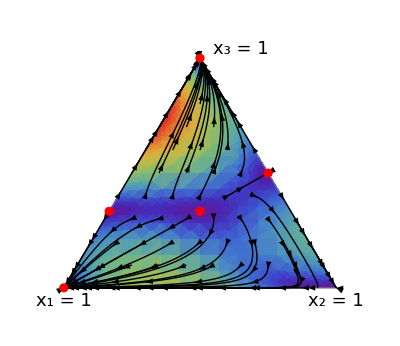

```mathematica
Show[{background,graphWithTrajectories,Graphics[listOfArrows],Graphics[{EdgeForm[Thick],Red,(Disk[Simplex2DCoord[#],0.015]&)/@({x1,x2,x3}/.{ToRules[criticalPoints]})}],Graphics[{
Inset[Style[Row[{Subscript[Style["x",Italic], 3]," = 1"}],18],{0.65,0.9}],
Inset[Style[Row[{Subscript[Style["x",Italic], 1]," = 1"}],18],{0,-0.05}],
Inset[Style[Row[{Subscript[Style["x",Italic], 2]," = 1"}],18],{1,-0.05}]}]
},PlotRange->{{-0.1,1+0.1},{-0.1,(√3)/2+0.1}},Frame->False,Axes->False,ImageSize->Full]
```

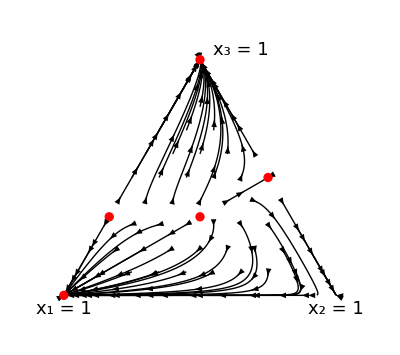

```mathematica
Show[{graphWithTrajectories,Graphics[listOfArrows],Graphics[{EdgeForm[Thick],Red,(Disk[Simplex2DCoord[#],0.015]&)/@({x1,x2,x3}/.{ToRules[criticalPoints]})}],Graphics[{
Inset[Style[Row[{Subscript[Style["x",Italic], 3]," = 1"}],18],{0.65,0.9}],
Inset[Style[Row[{Subscript[Style["x",Italic], 1]," = 1"}],18],{0,-0.05}],
Inset[Style[Row[{Subscript[Style["x",Italic], 2]," = 1"}],18],{1,-0.05}]}]
},PlotRange->{{-0.1,1+0.1},{-0.1,(√3)/2+0.1}},Frame->False,Axes->False,ImageSize->Full]
```

```mathematica
Export["~/projects/grnpm/gamesimplex.pdf",%,"PDF"]
```

~/projects/grnpm/gamesimplex.pdf

```mathematica
Column[{
Text@Style["critical points",Red,Bold,12],
Text[Row[{TableForm[{x1,x2,x3}//.List[ToRules[N[criticalPoints]]],TableHeadings->{None,{Style[Subscript[Style["x",Italic], 1],12],Style[Subscript[Style["x",Italic], 2],12],Style["x_3",12]}},TableSpacing->{1,1},TableAlignments->{Left,Bottom}],
TableForm[Map[Eigenvalues[Jacob[#,A,mutationMatrix]]&,{x1,x2}//.List[ToRules[N[criticalPoints]]]],TableHeadings->{None,{Style["λ_1",12],Style["λ_2",12]}},TableSpacing->{1,1},TableAlignments->{Right,Bottom}]},"   "],BaseStyle->{15}]},Alignment->Center,Spacings->1,Frame->True]
```

critical points
      x_1 | x_2 | x_3
0.333333 | 0.333333 | 0.333333
0.000100013 | 0.49995 | 0.49995
0.999867 | 0.0000666733 | 0.0000666733
0.0000500038 | 0.000100005 | 0.99985
0.666528 | 0.000166675 | 0.333306λ_1 | λ_2
0.333167 | 0.333167
0.4998 | -0.499733
-0.9997 | -0.999567
-1.99933 | -0.999583
0.666341 | -0.333113